```mathematica
ClearAll["Global`*"]
<< HPL`;
```

Package HPL already loaded...

$Aborted

Extract equations (B.5) - (B.7) from [Vogt, Moch: “The third-order QCD corrections to deep-inelastic scattering by photon exchange” ,Nucl. Phys. B, 724 (1-2), 3, 2005] with the help of ChatGPT

```mathematica
pqq[x_]:=2/(1-x)-1-x;
pqg[x_]:=1-2 x+2 x^2;
pgq[x_]:=(2 x-1)/(-2+x);
pgg[x_]:=1/(1-x)+1/x-2+x-x^2;

c2ns2[x_]:=CF*(CF-CA/2)*((8/5)*(9*pqg[-x]*(1-x)+pgq[-x]*(1-x^-1)+(37+17*x))*HPL[{-1,0},x]+4*pqq[-x]*(7*Zeta3+6*HPL[{-2,0},x]+4*HPL[{-1,2},x]-8*HPL[{-1,-1,0},x]+10*HPL[{-1,0,0},x]-3*HPL[{0,0,0},x]-8*HPL[{-1},x]*Zeta2-2*HPL[{0},x]+2*HPL[{0},x]*Zeta2-2*HPL[{3},x])-(72/5)*pqg[x]*((1+x)*(Zeta2-HPL[{0,0},x])-1-HPL[{0},x])+(8/5)*pgq[x]*(1-HPL[{0},x])+8*(1-5*x)*(HPL[{1,0,0},x]-HPL[{1},x]*Zeta2)-8*(1+5*x)*(2*HPL[{-1,-1,0},x]-HPL[{-1,0,0},x]+HPL[{-1},x]*Zeta2))+CF*nf*(1/54*pqq[x]*(247-144*Zeta2+180*HPL[{0,0},x]+72*HPL[{1,0},x]+72*HPL[{1,1},x]+342*HPL[{0},x]+174*HPL[{1},x]+144*HPL[{2},x])-1/3*(7+19*x)*HPL[{0},x]-1/3*(1+13*x)*HPL[{1},x]-1/18*(23+243*x)+DiracDelta[1-x]*(457/36+4/3*Zeta3+38/3*Zeta2))+CF^2*(16*HPL[{-2,0},x]+1/5*(33+37*x)*HPL[{0,0},x]+1/4*pqq[x]*(51+128*Zeta3+48*Zeta2+96*HPL[{-2,0},x]-12*HPL[{0,0},x]-72*HPL[{1,0},x]-72*HPL[{1,1},x]-96*HPL[{1,2},x]-96*HPL[{2,0},x]-112*HPL[{2,1},x]-32*HPL[{0,0,0},x]-48*HPL[{1,0,0},x]-128*HPL[{1,1,0},x]-96*HPL[{1,1,1},x]+122*HPL[{0},x]+96*HPL[{0},x]*Zeta2+54*HPL[{1},x]+32*HPL[{1},x]*Zeta2-48*HPL[{2},x]-96*HPL[{3},x])-1/2*(43+63*x)*HPL[{0},x]+1/2*(59-109*x)*HPL[{1},x]-4*(1-19*x)*Zeta3+2*(1+x)*(7*HPL[{1,0},x]+2*HPL[{2,0},x]+2*HPL[{2,1},x]+5*HPL[{0,0,0},x]-4*HPL[{0},x]*Zeta2+4*HPL[{3},x])+2*(5+9*x)*(HPL[{1,1},x]+2*HPL[{2},x])-4/5*(7+13*x)*Zeta2-1/4*(93+209*x)+DiracDelta[1-x]*(331/8-78*Zeta3+69*Zeta2+6*Zeta2^2))+CA*CF*(-1/108*pqq[x]*(3155-216*Zeta3-1584*Zeta2+1296*HPL[{-2,0},x]+1980*HPL[{0,0},x]+792*HPL[{1,0},x]+792*HPL[{1,1},x]+432*HPL[{1,2},x]+648*HPL[{0,0,0},x]+864*HPL[{1,0,0},x]-432*HPL[{1,1,0},x]+4302*HPL[{0},x]-432*HPL[{0},x]*Zeta2+2202*HPL[{1},x]-1296*HPL[{1},x]*Zeta2+1584*HPL[{2},x]+432*HPL[{3},x])+1/6*(71+323*x)*HPL[{0},x]-17/6*(5-19*x)*HPL[{1},x]-4/5*(9+16*x)*(Zeta2-HPL[{0,0},x])+1/36*(139+3159*x)-8*(5*Zeta3*x+HPL[{-2,0},x])-DiracDelta[1-x]*(5465/72-140/3*Zeta3+251/3*Zeta2-71/5*Zeta2^2));

c2ps2[x_]:=Module[{},CF*(8/3*(-pqg[-x]+pgq[-x])*HPL[{-1,0},x]+8/27*pqg[x]*(28+27*Zeta2-36*HPL[{0,0},x]-9*HPL[{1,0},x]-9*HPL[{1,1},x]-24*HPL[{0},x]+6*HPL[{1},x]-27*HPL[{2},x])+4/27*pgq[x]*(43-18*Zeta2+18*HPL[{1,0},x]+18*HPL[{1,1},x]-39*HPL[{1},x])+8/9*(71-49*x)*HPL[{0},x]+4/3*(16-13*x)*HPL[{1},x]+8*(1-2*x)*HPL[{2},x]+12*(1-x)*(HPL[{1,0},x]+HPL[{1,1},x])-2/3*(1+x)*(12*Zeta3+12*HPL[{-1,0},x]-13*HPL[{0,0},x]-12*HPL[{2,0},x]-12*HPL[{2,1},x]-30*HPL[{0,0,0},x]+24*HPL[{0},x]*Zeta2-24*HPL[{3},x])+22/3*(3-5*x)-8/3*(5-x)*Zeta2)
];


c2g2[x_]:=Module[{},CF*((4/15)*(pgq[-x]*(1-x^-1)+(217+117*x))*HPL[{-1,0},x]+1/15*(639-1004*x)*HPL[{0,0},x]-(8/5)*pqg[-x]*(6*(1-x)*HPL[{-1,0},x]-5*(2*HPL[{-2,0},x]-2*HPL[{-1,-1,0},x]+HPL[{-1,0,0},x]-HPL[{-1},x]*Zeta2))+(2/5)*pqg[x]*(6*(19+4*x)*(Zeta2-HPL[{0,0},x])-(9-90*Zeta3+90*HPL[{1,0},x]+90*HPL[{1,1},x]+60*HPL[{1,2},x]+40*HPL[{2,0},x]+50*HPL[{2,1},x]+50*HPL[{0,0,0},x]+30*HPL[{1,0,0},x]+40*HPL[{1,1,0},x]+50*HPL[{1,1,1},x]+54*HPL[{0},x]-60*HPL[{0},x]*Zeta2+30*HPL[{1},x]-40*HPL[{1},x]*Zeta2+90*HPL[{2},x]+60*HPL[{3},x]))+(4/15)*pgq[x]*(1-HPL[{0},x])+1/3*(16-61*x)*HPL[{0},x]-2*(1-8*x)*HPL[{1},x]+4*(5-4*x)*HPL[{2},x]-4*(1-18*x)*Zeta3+2*(1-2*x)*(8*HPL[{-2,0},x]+2*HPL[{2,0},x]+2*HPL[{2,1},x]+5*HPL[{0,0,0},x]+4*HPL[{1,0,0},x]-4*HPL[{0},x]*Zeta2-4*HPL[{1},x]*Zeta2+4*HPL[{3},x])-8*(1+2*x)*(2*HPL[{-1,-1,0},x]-HPL[{-1,0,0},x]+HPL[{-1},x]*Zeta2)+2*(5+4*x)*(HPL[{1,0},x]+HPL[{1,1},x])-(4/15)*(111-176*x)*Zeta2-1/3*(117-121*x))+CA*((8/3)*(pgq[-x]-3*(4+3*x))*HPL[{-1,0},x]+(4/3)*HPL[{0,0},x]*(47+35*x)+2*(23-6*x)*HPL[{1,0},x]+6*(7-2*x)*HPL[{1,1},x]+4*(5+14*x)*HPL[{0,0,0},x]+(4/3)*pqg[-x]*(6*HPL[{-2,0},x]+10*HPL[{-1,0},x]+6*HPL[{-1,2},x]+9*HPL[{-1,0,0},x]-6*HPL[{-1},x]*Zeta2)-1/54*pqg[x]*(4493-648*Zeta3-3996*Zeta2+3492*HPL[{0,0},x]+2412*HPL[{1,0},x]+2196*HPL[{1,1},x]+216*HPL[{1,2},x]+432*HPL[{2,0},x]+432*HPL[{2,1},x]+432*HPL[{1,0,0},x]+648*HPL[{1,1,0},x]+216*HPL[{1,1,1},x]+6270*HPL[{0},x]-432*HPL[{0},x]*Zeta2+4710*HPL[{1},x]-216*HPL[{1},x]*Zeta2+3996*HPL[{2},x]+432*HPL[{3},x])+(4/27)*pgq[x]*(43-18*Zeta2+18*HPL[{1,0},x]+18*HPL[{1,1},x]-39*HPL[{1},x])+1/9*(1567-338*x)*HPL[{0},x]+1/3*(289-52*x)*HPL[{1},x]+2*(33-2*x)*HPL[{2},x]-4*(1-2*x)*(HPL[{1,0,0},x]-HPL[{1},x]*Zeta2)-4*(1+2*x)*(2*HPL[{-2,0},x]-2*HPL[{-1,-1,0},x]+HPL[{-1,0,0},x]-HPL[{-1},x]*Zeta2)-8*(1+3*x)*(Zeta3+2*HPL[{0},x]*Zeta2-2*HPL[{3},x])+8*(1+4*x)*(HPL[{2,0},x]+HPL[{2,1},x])+7/6*(105-46*x)-2/3*(107-10*x)*Zeta2)];
```

Compare to equations (4.8) - (4.10) from the same paper.

```mathematica
L0[x]:=Log[x];
L1[x]:=Log[1-x];
D0[x]:=1/(1-x);
D1[x]:=L1[x]/(1-x);
D2[x]:=L1[x]^2/(1-x);
D3[x]:=L1[x]^3/(1-x);

c2ns2appr[x_]=Module[{},
128/9*D3[x]-184/3*D2[x]-31.1052*D1[x]+188.641*D0[x]-338.513*DiracDelta[1-x]
-17.74*L1[x]^3+72.24*L1[x]^2-628.8*L1[x]-181.0-806.7*x+0.719*x*L0[x]^4
+L0[x]*L1[x]*(37.75*L0[x]-147.1*L1[x])-28.384*L0[x]-20.70*L0[x]^2-80/27*L0[x]^3
+nf*(
16/9*D2[x]-232/27*D1[x]+6.34888*D0[x]+46.8531*DiracDelta[1-x]-1.500*L1[x]^2
+24.87*L1[x]-7.8109-17.82*x-12.97*x^2-0.185*x*L0[x]^3+8.113*L0[x]*L1[x]
+16/3*L0[x]+20/9*L0[x]^2
)
];

c2ns2regappr[x_]=Module[{},
-17.74*L1[x]^3+72.24*L1[x]^2-628.8*L1[x]-181.0-806.7*x+0.719*x*L0[x]^4
+L0[x]*L1[x]*(37.75*L0[x]-147.1*L1[x])-28.384*L0[x]-20.70*L0[x]^2-80/27*L0[x]^3
+nf*(
-1.500*L1[x]^2
+24.87*L1[x]-7.8109-17.82*x-12.97*x^2-0.185*x*L0[x]^3+8.113*L0[x]*L1[x]
+16/3*L0[x]+20/9*L0[x]^2
)
];

c2ns2plusappr[x_]=Module[{},
128/9*D3[x]-184/3*D2[x]-31.1052*D1[x]+188.641*D0[x]
+nf*(
16/9*D2[x]-232/27*D1[x]+6.34888*D0[x]
)
];

c2ns2localappr[x_]=Module[{},
-338.513*DiracDelta[1-x]
+nf*(
46.8531*DiracDelta[1-x]
)
];

c2g2appr[x_]=Module[{},
58/9*L1[x]^3-24*L1[x]^2-34.88*L1[x]+30.586-(25.08+760.3*x
+29.65*L1[x]^3)*(1-x)+1204*x*L0[x]^2+L0[x]*L1[x]*(293.8+711.2*x+1043*L0[x])
+115.6*L0[x]-7.109*L0[x]^2+70/9*L0[x]^3+11.9033*(1-x)/x
];

c2ps2appr[x_]=Module[{},
(8/3*L1[x]^2-32/3*L1[x]+9.8937)*(1-x)+(9.57-13.41*x+0.08*L1[x]^3)*(1-x)^2
+5.667*x*L0[x]^3-L0[x]^2*L1[x]*(20.26-33.93*x)+43.36*(1-x)*L0[x]-1.053*L0[x]^2
+40/9*L0[x]^3+5.2903*(1-x)^2/x
];
```

```mathematica
c2ns2approld[x_]=Module[{},
14.2222* D3[x]−61.3333 *D2[x]−31.105 *D1[x]+188.64*D0[x]
−17.19 *L1[x]^3+71.08*L1[x]^2−660.7 *L1[x]+L1[x]*L0[x]*(−174.8 *L1[x]+95.09 *L0[x])
−2.835 *L0[x]^3−17.08 *L0[x]^2 +5.986 *L0[x]−1008* x−69.59−338.046 *DiracDelta[1−x]+
nf*(
1.77778 *D2[x]−8.5926 *D1[x]+6.3489*D0[x]
−1.707 *L1[x]^2+22.95 *L1[x]+L1[x]*L0[x](3.036 *L0[x]+17.97) 
+2.244 *L0[x]^2+5.770* L0[x]−37.91* x−5.691+46.8405 *DiracDelta[1-x]
)
];

c2ps2approld[x_]=Module[{},
-0.101*(1-x)*L1[x]^3-(24.75-13.80*x)*L1[x]*L0[x]^2+30.23*L1[x]*L0[x]
+4.310*L0[x]^3-2.086*L0[x]^2+39.78*L0[x]+5.290*(1/x-1)
];

c2g2approld[x_]=Module[{},
(6.445+209.4*(1-x))*L1[x]^3-24.00*L1[x]^2+(1494/x-1483)*L1[x]
+L1[x]*L0[x]*(-871.8*L1[x]-724.1*L0[x])+5.319*L0[x]^3-59.48*L0[x]^2-284.8*L0[x]
+11.90/x+392.4-0.28*DiracDelta[1-x]
];
```

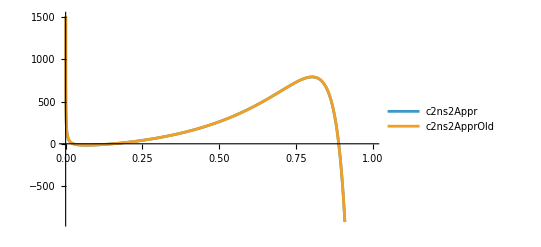

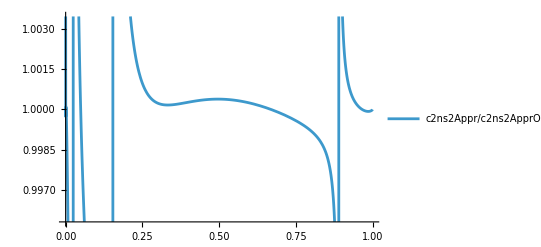

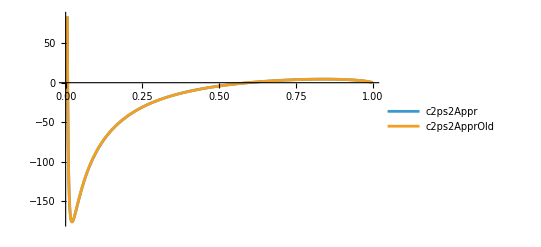

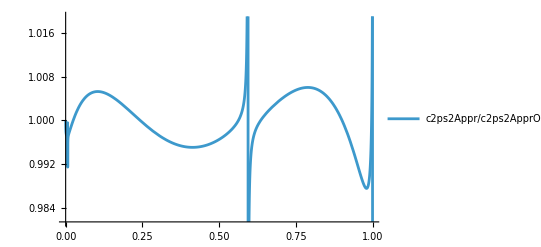

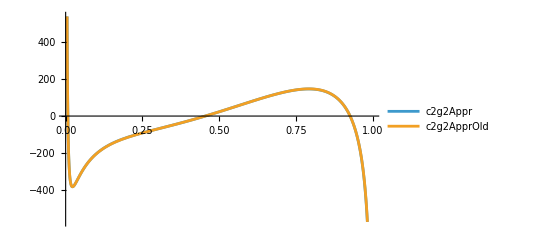

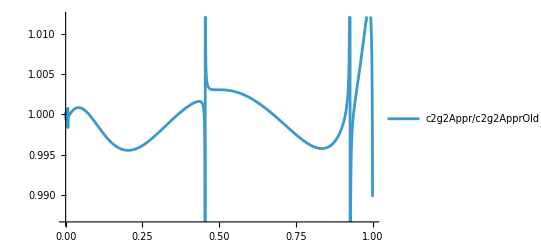

```mathematica
Plot[{
c2ns2appr[x]/.nf->3,
c2ns2approld[x]/.nf->3
},
{x,0,1},PlotLegends->{"c2ns2Appr","c2ns2ApprOld"}]
Plot[{
c2ns2appr[x]/c2ns2approld[x]/.nf->3
},
{x,0,1},PlotLegends->{"c2ns2Appr/c2ns2ApprOld"}]
Plot[{
c2ps2appr[x]/.nf->3,
c2ps2approld[x]/.nf->3
},
{x,0,1},PlotLegends->{"c2ps2Appr","c2ps2ApprOld"}]
Plot[{
c2ps2appr[x]/c2ps2approld[x]/.nf->3
},
{x,0,1},PlotLegends->{"c2ps2Appr/c2ps2ApprOld"}]
Plot[{
c2g2appr[x]/.nf->3,
c2g2approld[x]/.nf->3
},
{x,0,1},PlotLegends->{"c2g2Appr","c2g2ApprOld"}]
Plot[{
c2g2appr[x]/c2g2approld[x]/.nf->3
},
{x,0,1},PlotLegends->{"c2g2Appr/c2g2ApprOld"}]
```

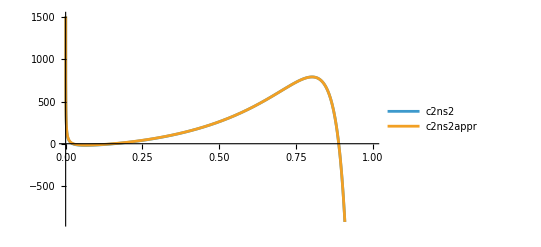

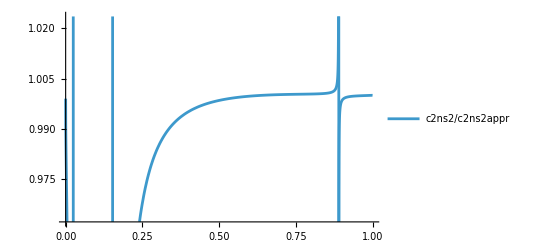

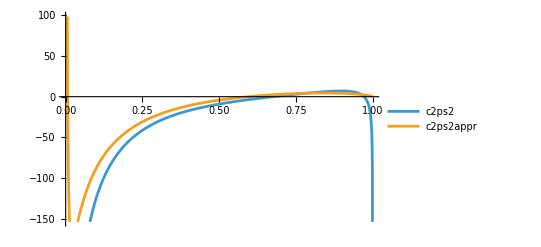

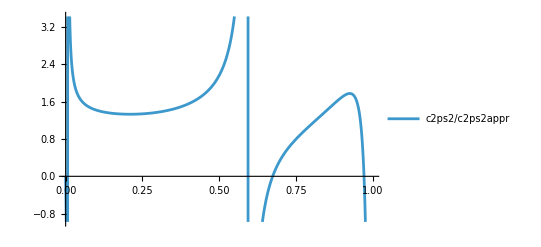

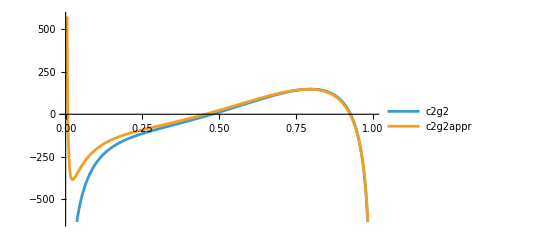

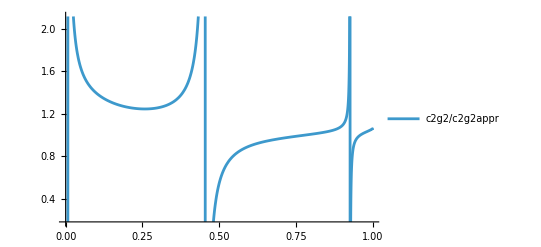

```mathematica
Plot[{
c2ns2[x]/.{nf->3,DiracDelta[x]->0,Zeta2->Zeta[2],Zeta3->Zeta[3],CF->4/3,CA->3},
c2ns2appr[x]/.{nf->3,DiracDelta[x]->0,Zeta2->Zeta[2],Zeta3->Zeta[3]}
},{x,0,1},PlotLegends->{"c2ns2","c2ns2appr"}]
Plot[
(c2ns2[x]/c2ns2appr[x])/.{nf->3,DiracDelta[x]->0,Zeta2->Zeta[2],Zeta3->Zeta[3],CF->4/3,CA->3}
,{x,0,1},PlotLegends->{"c2ns2/c2ns2appr"}]
Plot[{
c2ps2[x]/.{Zeta2->Zeta[2],Zeta3->Zeta[3],CF->4/3,CA->3},
c2ps2appr[x]/.{Zeta2->Zeta[2],Zeta3->Zeta[3]}
},{x,0,1},PlotLegends->{"c2ps2","c2ps2appr"}]
Plot[
(c2ps2[x]/c2ps2appr[x])/.{Zeta2->Zeta[2],Zeta3->Zeta[3],CF->4/3,CA->3}
,{x,0,1},PlotLegends->{"c2ps2/c2ps2appr"}]
Plot[{
c2g2[x]/.{Zeta2->Zeta[2],Zeta3->Zeta[3],CF->4/3,CA->3},
c2g2appr[x]/.{Zeta2->Zeta[2],Zeta3->Zeta[3]}
},{x,0,1},PlotLegends->{"c2g2","c2g2appr"}]
Plot[
(c2g2[x]/c2g2appr[x])/.{Zeta2->Zeta[2],Zeta3->Zeta[3],CF->4/3,CA->3}
,{x,0,1},PlotLegends->{"c2g2/c2g2appr"}]
```

This seems to match! Now let us rewrite the coefficient function c2ns2 in form that we can put into openQCDrad...

```mathematica
c2ns2x=Collect[c2ns2[x],
{1/(1-x),DiracDelta[1-x],nf}]/.HPL[a_List,x_]:>myHPL[HPLMtoA[a],x]/.myHPL[a_List,x_]:>With[{n=Length[a]},Symbol["HPL"<>ToString[n]][Sequence@@a,x]];
c2ns2xforcode=c2ns2x/.{
x->z
}
CForm[c2ns2xforcode]
```

1/4 CF^2 (-93-209 z)+1/36 CA CF (139+3159 z)-4/5 CF^2 (7+13 z) Zeta2-4 CF^2 (1-19 z) Zeta3+(CF^2 (331/8+69 Zeta2+6 Zeta2^2-78 Zeta3)-CA CF (5465/72+(251 Zeta2)/3-(71 Zeta2^2)/5-(140 Zeta3)/3)+CF nf (457/36+(38 Zeta2)/3+(4 Zeta3)/3)) DiracDelta[-1+z]+(8 CF (-CA/2+CF) (-1+2 z) (1-HPL1[0,z]))/(5 (-2+z))-1/2 CF^2 (43+63 z) HPL1[0,z]+1/6 CA CF (71+323 z) HPL1[0,z]+1/2 CF^2 (59-109 z) HPL1[1,z]-17/6 CA CF (5-19 z) HPL1[1,z]+296/5 CF (-CA/2+CF) HPL2[-1,0,z]+(8 CF (-CA/2+CF) (1-1/z) (-1-2 z) HPL2[-1,0,z])/(5 (-2-z))+136/5 CF (-CA/2+CF) z HPL2[-1,0,z]+72/5 CF (-CA/2+CF) (1-z) (1+2 z+2 z^2) HPL2[-1,0,z]-72/5 CF (-CA/2+CF) (1-2 z+2 z^2) (-1-HPL1[0,z]+(1+z) (Zeta2-HPL2[0,0,z]))-4/5 CA CF (9+16 z) (Zeta2-HPL2[0,0,z])+1/5 CF^2 (33+37 z) HPL2[0,0,z]+2 CF^2 (5+9 z) (2 HPL2[0,1,z]+HPL2[1,1,z])+nf (1/18 CF (-23-243 z)-1/3 CF (7+19 z) HPL1[0,z]-1/3 CF (1+13 z) HPL1[1,z]+1/54 CF (-247+144 Zeta2-342 HPL1[0,z]-174 HPL1[1,z]-180 HPL2[0,0,z]-144 HPL2[0,1,z]-72 HPL2[1,0,z]-72 HPL2[1,1,z])-1/54 CF z (247-144 Zeta2+342 HPL1[0,z]+174 HPL1[1,z]+180 HPL2[0,0,z]+144 HPL2[0,1,z]+72 HPL2[1,0,z]+72 HPL2[1,1,z]))-8 CF (-CA/2+CF) (1+5 z) (Zeta2 HPL1[-1,z]+2 HPL3[-1,-1,0,z]-HPL3[-1,0,0,z])+16 CF^2 HPL3[0,-1,0,z]-8 CA CF (5 z Zeta3+HPL3[0,-1,0,z])+4 CF (-CA/2+CF) (-1+z+2/(1+z)) (7 Zeta3-8 Zeta2 HPL1[-1,z]-2 HPL1[0,z]+2 Zeta2 HPL1[0,z]-8 HPL3[-1,-1,0,z]+10 HPL3[-1,0,0,z]+4 HPL3[-1,0,1,z]+6 HPL3[0,-1,0,z]-3 HPL3[0,0,0,z]-2 HPL3[0,0,1,z])+2 CF^2 (1+z) (-4 Zeta2 HPL1[0,z]+7 HPL2[1,0,z]+5 HPL3[0,0,0,z]+4 HPL3[0,0,1,z]+2 HPL3[0,1,0,z]+2 HPL3[0,1,1,z])+8 CF (-CA/2+CF) (1-5 z) (-Zeta2 HPL1[1,z]+HPL3[1,0,0,z])+1/108 CA CF (3155-1584 Zeta2-216 Zeta3+4302 HPL1[0,z]-432 Zeta2 HPL1[0,z]+2202 HPL1[1,z]-1296 Zeta2 HPL1[1,z]+1980 HPL2[0,0,z]+1584 HPL2[0,1,z]+792 HPL2[1,0,z]+792 HPL2[1,1,z]+1296 HPL3[0,-1,0,z]+648 HPL3[0,0,0,z]+432 HPL3[0,0,1,z]+864 HPL3[1,0,0,z]+432 HPL3[1,0,1,z]-432 HPL3[1,1,0,z])-1/108 CA CF z (-3155+1584 Zeta2+216 Zeta3-4302 HPL1[0,z]+432 Zeta2 HPL1[0,z]-2202 HPL1[1,z]+1296 Zeta2 HPL1[1,z]-1980 HPL2[0,0,z]-1584 HPL2[0,1,z]-792 HPL2[1,0,z]-792 HPL2[1,1,z]-1296 HPL3[0,-1,0,z]-648 HPL3[0,0,0,z]-432 HPL3[0,0,1,z]-864 HPL3[1,0,0,z]-432 HPL3[1,0,1,z]+432 HPL3[1,1,0,z])+1/(1-z)(1/27 CF nf (247-144 Zeta2+342 HPL1[0,z]+174 HPL1[1,z]+180 HPL2[0,0,z]+144 HPL2[0,1,z]+72 HPL2[1,0,z]+72 HPL2[1,1,z])+1/54 CA CF (-3155+1584 Zeta2+216 Zeta3-4302 HPL1[0,z]+432 Zeta2 HPL1[0,z]-2202 HPL1[1,z]+1296 Zeta2 HPL1[1,z]-1980 HPL2[0,0,z]-1584 HPL2[0,1,z]-792 HPL2[1,0,z]-792 HPL2[1,1,z]-1296 HPL3[0,-1,0,z]-648 HPL3[0,0,0,z]-432 HPL3[0,0,1,z]-864 HPL3[1,0,0,z]-432 HPL3[1,0,1,z]+432 HPL3[1,1,0,z])+1/2 CF^2 (51+48 Zeta2+128 Zeta3+122 HPL1[0,z]+96 Zeta2 HPL1[0,z]+54 HPL1[1,z]+32 Zeta2 HPL1[1,z]-12 HPL2[0,0,z]-48 HPL2[0,1,z]-72 HPL2[1,0,z]-72 HPL2[1,1,z]+96 HPL3[0,-1,0,z]-32 HPL3[0,0,0,z]-96 HPL3[0,0,1,z]-96 HPL3[0,1,0,z]-112 HPL3[0,1,1,z]-48 HPL3[1,0,0,z]-96 HPL3[1,0,1,z]-128 HPL3[1,1,0,z]-96 HPL3[1,1,1,z]))-1/4 CF^2 z (51+48 Zeta2+128 Zeta3+122 HPL1[0,z]+96 Zeta2 HPL1[0,z]+54 HPL1[1,z]+32 Zeta2 HPL1[1,z]-12 HPL2[0,0,z]-48 HPL2[0,1,z]-72 HPL2[1,0,z]-72 HPL2[1,1,z]+96 HPL3[0,-1,0,z]-32 HPL3[0,0,0,z]-96 HPL3[0,0,1,z]-96 HPL3[0,1,0,z]-112 HPL3[0,1,1,z]-48 HPL3[1,0,0,z]-96 HPL3[1,0,1,z]-128 HPL3[1,1,0,z]-96 HPL3[1,1,1,z])+1/4 CF^2 (-51-48 Zeta2-128 Zeta3-122 HPL1[0,z]-96 Zeta2 HPL1[0,z]-54 HPL1[1,z]-32 Zeta2 HPL1[1,z]+12 HPL2[0,0,z]+48 HPL2[0,1,z]+72 HPL2[1,0,z]+72 HPL2[1,1,z]-96 HPL3[0,-1,0,z]+32 HPL3[0,0,0,z]+96 HPL3[0,0,1,z]+96 HPL3[0,1,0,z]+112 HPL3[0,1,1,z]+48 HPL3[1,0,0,z]+96 HPL3[1,0,1,z]+128 HPL3[1,1,0,z]+96 HPL3[1,1,1,z])

(Power(CF,2)*(-93 - 209*z))/4. + (CA*CF*(139 + 3159*z))/36. - (4*Power(CF,2)*(7 + 13*z)*Zeta2)/5. - 4*Power(CF,2)*(1 - 19*z)*Zeta3 + 
   (Power(CF,2)*(41.375 + 69*Zeta2 + 6*Power(Zeta2,2) - 78*Zeta3) - CA*CF*(75.90277777777777 + (251*Zeta2)/3. - (71*Power(Zeta2,2))/5. - (140*Zeta3)/3.) + 
      CF*nf*(12.694444444444445 + (38*Zeta2)/3. + (4*Zeta3)/3.))*DiracDelta(-1 + z) + (8*CF*(-0.5*CA + CF)*(-1 + 2*z)*(1 - HPL1(0,z)))/(5.*(-2 + z)) - (Power(CF,2)*(43 + 63*z)*HPL1(0,z))/2. + 
   (CA*CF*(71 + 323*z)*HPL1(0,z))/6. + (Power(CF,2)*(59 - 109*z)*HPL1(1,z))/2. - (17*CA*CF*(5 - 19*z)*HPL1(1,z))/6. + (296*CF*(-0.5*CA + CF)*HPL2(-1,0,z))/5. + 
   (8*CF*(-0.5*CA + CF)*(1 - 1/z)*(-1 - 2*z)*HPL2(-1,0,z))/(5.*(-2 - z)) + (136*CF*(-0.5*CA + CF)*z*HPL2(-1,0,z))/5. + (72*CF*(-0.5*CA + CF)*(1 - z)*(1 + 2*z + 2*Power(z,2))*HPL2(-1,0,z))/5. - 
   (72*CF*(-0.5*CA + CF)*(1 - 2*z + 2*Power(z,2))*(-1 - HPL1(0,z) + (1 + z)*(Zeta2 - HPL2(0,0,z))))/5. - (4*CA*CF*(9 + 16*z)*(Zeta2 - HPL2(0,0,z)))/5. + (Power(CF,2)*(33 + 37*z)*HPL2(0,0,z))/5. + 
   2*Power(CF,2)*(5 + 9*z)*(2*HPL2(0,1,z) + HPL2(1,1,z)) + nf*((CF*(-23 - 243*z))/18. - (CF*(7 + 19*z)*HPL1(0,z))/3. - (CF*(1 + 13*z)*HPL1(1,z))/3. + 
      (CF*(-247 + 144*Zeta2 - 342*HPL1(0,z) - 174*HPL1(1,z) - 180*HPL2(0,0,z) - 144*HPL2(0,1,z) - 72*HPL2(1,0,z) - 72*HPL2(1,1,z)))/54. - 
      (CF*z*(247 - 144*Zeta2 + 342*HPL1(0,z) + 174*HPL1(1,z) + 180*HPL2(0,0,z) + 144*HPL2(0,1,z) + 72*HPL2(1,0,z) + 72*HPL2(1,1,z)))/54.) - 
   8*CF*(-0.5*CA + CF)*(1 + 5*z)*(Zeta2*HPL1(-1,z) + 2*HPL3(-1,-1,0,z) - HPL3(-1,0,0,z)) + 16*Power(CF,2)*HPL3(0,-1,0,z) - 8*CA*CF*(5*z*Zeta3 + HPL3(0,-1,0,z)) + 
   4*CF*(-0.5*CA + CF)*(-1 + z + 2/(1 + z))*(7*Zeta3 - 8*Zeta2*HPL1(-1,z) - 2*HPL1(0,z) + 2*Zeta2*HPL1(0,z) - 8*HPL3(-1,-1,0,z) + 10*HPL3(-1,0,0,z) + 4*HPL3(-1,0,1,z) + 6*HPL3(0,-1,0,z) - 3*HPL3(0,0,0,z) - 
      2*HPL3(0,0,1,z)) + 2*Power(CF,2)*(1 + z)*(-4*Zeta2*HPL1(0,z) + 7*HPL2(1,0,z) + 5*HPL3(0,0,0,z) + 4*HPL3(0,0,1,z) + 2*HPL3(0,1,0,z) + 2*HPL3(0,1,1,z)) + 
   8*CF*(-0.5*CA + CF)*(1 - 5*z)*(-(Zeta2*HPL1(1,z)) + HPL3(1,0,0,z)) + (CA*CF*(3155 - 1584*Zeta2 - 216*Zeta3 + 4302*HPL1(0,z) - 432*Zeta2*HPL1(0,z) + 2202*HPL1(1,z) - 1296*Zeta2*HPL1(1,z) + 
        1980*HPL2(0,0,z) + 1584*HPL2(0,1,z) + 792*HPL2(1,0,z) + 792*HPL2(1,1,z) + 1296*HPL3(0,-1,0,z) + 648*HPL3(0,0,0,z) + 432*HPL3(0,0,1,z) + 864*HPL3(1,0,0,z) + 432*HPL3(1,0,1,z) - 432*HPL3(1,1,0,z)))/108.\
    - (CA*CF*z*(-3155 + 1584*Zeta2 + 216*Zeta3 - 4302*HPL1(0,z) + 432*Zeta2*HPL1(0,z) - 2202*HPL1(1,z) + 1296*Zeta2*HPL1(1,z) - 1980*HPL2(0,0,z) - 1584*HPL2(0,1,z) - 792*HPL2(1,0,z) - 792*HPL2(1,1,z) - 
        1296*HPL3(0,-1,0,z) - 648*HPL3(0,0,0,z) - 432*HPL3(0,0,1,z) - 864*HPL3(1,0,0,z) - 432*HPL3(1,0,1,z) + 432*HPL3(1,1,0,z)))/108. + 
   ((CF*nf*(247 - 144*Zeta2 + 342*HPL1(0,z) + 174*HPL1(1,z) + 180*HPL2(0,0,z) + 144*HPL2(0,1,z) + 72*HPL2(1,0,z) + 72*HPL2(1,1,z)))/27. + 
      (CA*CF*(-3155 + 1584*Zeta2 + 216*Zeta3 - 4302*HPL1(0,z) + 432*Zeta2*HPL1(0,z) - 2202*HPL1(1,z) + 1296*Zeta2*HPL1(1,z) - 1980*HPL2(0,0,z) - 1584*HPL2(0,1,z) - 792*HPL2(1,0,z) - 792*HPL2(1,1,z) - 
           1296*HPL3(0,-1,0,z) - 648*HPL3(0,0,0,z) - 432*HPL3(0,0,1,z) - 864*HPL3(1,0,0,z) - 432*HPL3(1,0,1,z) + 432*HPL3(1,1,0,z)))/54. + 
      (Power(CF,2)*(51 + 48*Zeta2 + 128*Zeta3 + 122*HPL1(0,z) + 96*Zeta2*HPL1(0,z) + 54*HPL1(1,z) + 32*Zeta2*HPL1(1,z) - 12*HPL2(0,0,z) - 48*HPL2(0,1,z) - 72*HPL2(1,0,z) - 72*HPL2(1,1,z) + 96*HPL3(0,-1,0,z) - 
           32*HPL3(0,0,0,z) - 96*HPL3(0,0,1,z) - 96*HPL3(0,1,0,z) - 112*HPL3(0,1,1,z) - 48*HPL3(1,0,0,z) - 96*HPL3(1,0,1,z) - 128*HPL3(1,1,0,z) - 96*HPL3(1,1,1,z)))/2.)/(1 - z) - 
   (Power(CF,2)*z*(51 + 48*Zeta2 + 128*Zeta3 + 122*HPL1(0,z) + 96*Zeta2*HPL1(0,z) + 54*HPL1(1,z) + 32*Zeta2*HPL1(1,z) - 12*HPL2(0,0,z) - 48*HPL2(0,1,z) - 72*HPL2(1,0,z) - 72*HPL2(1,1,z) + 96*HPL3(0,-1,0,z) - 
        32*HPL3(0,0,0,z) - 96*HPL3(0,0,1,z) - 96*HPL3(0,1,0,z) - 112*HPL3(0,1,1,z) - 48*HPL3(1,0,0,z) - 96*HPL3(1,0,1,z) - 128*HPL3(1,1,0,z) - 96*HPL3(1,1,1,z)))/4. + 
   (Power(CF,2)*(-51 - 48*Zeta2 - 128*Zeta3 - 122*HPL1(0,z) - 96*Zeta2*HPL1(0,z) - 54*HPL1(1,z) - 32*Zeta2*HPL1(1,z) + 12*HPL2(0,0,z) + 48*HPL2(0,1,z) + 72*HPL2(1,0,z) + 72*HPL2(1,1,z) - 96*HPL3(0,-1,0,z) + 
        32*HPL3(0,0,0,z) + 96*HPL3(0,0,1,z) + 96*HPL3(0,1,0,z) + 112*HPL3(0,1,1,z) + 48*HPL3(1,0,0,z) + 96*HPL3(1,0,1,z) + 128*HPL3(1,1,0,z) + 96*HPL3(1,1,1,z)))/4.

```mathematica
c2ps2x=Collect[c2ps2[x],
{1/(1-x),DiracDelta[1-x],nf}]/.HPL[a_List,x_]:>myHPL[HPLMtoA[a],x]/.myHPL[a_List,x_]:>With[{n=Length[a]},Symbol["HPL"<>ToString[n]][Sequence@@a,x]];
c2ps2xforcode=c2ps2x/.{
x->z
}
CForm[c2ps2xforcode]
```

12 CF nf (1-z) (HPL2[1,0,z]+HPL2[1,1,z])+CF nf (22/3 (3-5 z)-8/3 (5-z) Zeta2+8/9 (71-49 z) HPL1[0,z]+4/3 (16-13 z) HPL1[1,z]+8/3 (-1+(-1-2 z)/(-2-z)-2 z-2 z^2) HPL2[-1,0,z]+8 (1-2 z) HPL2[0,1,z]+8/27 (1-2 z+2 z^2) (28+27 Zeta2-24 HPL1[0,z]+6 HPL1[1,z]-36 HPL2[0,0,z]-27 HPL2[0,1,z]-9 HPL2[1,0,z]-9 HPL2[1,1,z])+(4 (-1+2 z) (43-18 Zeta2-39 HPL1[1,z]+18 HPL2[1,0,z]+18 HPL2[1,1,z]))/(27 (-2+z))-2/3 (1+z) (12 Zeta3+24 Zeta2 HPL1[0,z]+12 HPL2[-1,0,z]-13 HPL2[0,0,z]-30 HPL3[0,0,0,z]-24 HPL3[0,0,1,z]-12 HPL3[0,1,0,z]-12 HPL3[0,1,1,z]))

12*CF*nf*(1 - z)*(HPL2(1,0,z) + HPL2(1,1,z)) + CF*nf*((22*(3 - 5*z))/3. - (8*(5 - z)*Zeta2)/3. + (8*(71 - 49*z)*HPL1(0,z))/9. + (4*(16 - 13*z)*HPL1(1,z))/3. + 
      (8*(-1 + (-1 - 2*z)/(-2 - z) - 2*z - 2*Power(z,2))*HPL2(-1,0,z))/3. + 8*(1 - 2*z)*HPL2(0,1,z) + 
      (8*(1 - 2*z + 2*Power(z,2))*(28 + 27*Zeta2 - 24*HPL1(0,z) + 6*HPL1(1,z) - 36*HPL2(0,0,z) - 27*HPL2(0,1,z) - 9*HPL2(1,0,z) - 9*HPL2(1,1,z)))/27. + 
      (4*(-1 + 2*z)*(43 - 18*Zeta2 - 39*HPL1(1,z) + 18*HPL2(1,0,z) + 18*HPL2(1,1,z)))/(27.*(-2 + z)) - 
      (2*(1 + z)*(12*Zeta3 + 24*Zeta2*HPL1(0,z) + 12*HPL2(-1,0,z) - 13*HPL2(0,0,z) - 30*HPL3(0,0,0,z) - 24*HPL3(0,0,1,z) - 12*HPL3(0,1,0,z) - 12*HPL3(0,1,1,z)))/3.)

```mathematica
(*The nf is factored out in openQCDrad*)
c2g2x=Collect[c2g2[x]/nf,
{1/(1-x),DiracDelta[1-x],nf}]/.HPL[a_List,x_]:>myHPL[HPLMtoA[a],x]/.myHPL[a_List,x_]:>With[{n=Length[a]},Symbol["HPL"<>ToString[n]][Sequence@@a,x]];
c2g2xforcode=c2g2x/.{
x->z
}
CForm[c2g2xforcode]
```

1/3 CF (-117+121 z)-4/15 CF (111-176 z) Zeta2-4 CF (1-18 z) Zeta3+(4 CF (-1+2 z) (1-HPL1[0,z]))/(15 (-2+z))+1/3 CF (16-61 z) HPL1[0,z]-2 CF (1-8 z) HPL1[1,z]+4/15 CF (217+((1-1/z) (-1-2 z))/(-2-z)+117 z) HPL2[-1,0,z]-48/5 CF (1-z) (1+2 z+2 z^2) HPL2[-1,0,z]+1/15 CF (639-1004 z) HPL2[0,0,z]+4 CF (5-4 z) HPL2[0,1,z]+2 CF (5+4 z) (HPL2[1,0,z]+HPL2[1,1,z])-8 CF (1+2 z) (Zeta2 HPL1[-1,z]+2 HPL3[-1,-1,0,z]-HPL3[-1,0,0,z])+8 CF (1+2 z+2 z^2) (-Zeta2 HPL1[-1,z]-2 HPL3[-1,-1,0,z]+HPL3[-1,0,0,z]+2 HPL3[0,-1,0,z])+2 CF (1-2 z) (-4 Zeta2 HPL1[0,z]-4 Zeta2 HPL1[1,z]+8 HPL3[0,-1,0,z]+5 HPL3[0,0,0,z]+4 HPL3[0,0,1,z]+2 HPL3[0,1,0,z]+2 HPL3[0,1,1,z]+4 HPL3[1,0,0,z])+2/5 CF (1-2 z+2 z^2) (-9+90 Zeta3-54 HPL1[0,z]+60 Zeta2 HPL1[0,z]-30 HPL1[1,z]+40 Zeta2 HPL1[1,z]+6 (19+4 z) (Zeta2-HPL2[0,0,z])-90 HPL2[0,1,z]-90 HPL2[1,0,z]-90 HPL2[1,1,z]-50 HPL3[0,0,0,z]-60 HPL3[0,0,1,z]-40 HPL3[0,1,0,z]-50 HPL3[0,1,1,z]-30 HPL3[1,0,0,z]-60 HPL3[1,0,1,z]-40 HPL3[1,1,0,z]-50 HPL3[1,1,1,z])+CA (7/6 (105-46 z)-2/3 (107-10 z) Zeta2+1/9 (1567-338 z) HPL1[0,z]+1/3 (289-52 z) HPL1[1,z]+8/3 ((-1-2 z)/(-2-z)-3 (4+3 z)) HPL2[-1,0,z]+4/3 (47+35 z) HPL2[0,0,z]+2 (33-2 z) HPL2[0,1,z]+2 (23-6 z) HPL2[1,0,z]+6 (7-2 z) HPL2[1,1,z]+(4 (-1+2 z) (43-18 Zeta2-39 HPL1[1,z]+18 HPL2[1,0,z]+18 HPL2[1,1,z]))/(27 (-2+z))-4 (1+2 z) (-Zeta2 HPL1[-1,z]-2 HPL3[-1,-1,0,z]+HPL3[-1,0,0,z]+2 HPL3[0,-1,0,z])+4/3 (1+2 z+2 z^2) (-6 Zeta2 HPL1[-1,z]+10 HPL2[-1,0,z]+9 HPL3[-1,0,0,z]+6 HPL3[-1,0,1,z]+6 HPL3[0,-1,0,z])+4 (5+14 z) HPL3[0,0,0,z]-8 (1+3 z) (Zeta3+2 Zeta2 HPL1[0,z]-2 HPL3[0,0,1,z])+8 (1+4 z) (HPL3[0,1,0,z]+HPL3[0,1,1,z])-4 (1-2 z) (-Zeta2 HPL1[1,z]+HPL3[1,0,0,z])-1/54 (1-2 z+2 z^2) (4493-3996 Zeta2-648 Zeta3+6270 HPL1[0,z]-432 Zeta2 HPL1[0,z]+4710 HPL1[1,z]-216 Zeta2 HPL1[1,z]+3492 HPL2[0,0,z]+3996 HPL2[0,1,z]+2412 HPL2[1,0,z]+2196 HPL2[1,1,z]+432 HPL3[0,0,1,z]+432 HPL3[0,1,0,z]+432 HPL3[0,1,1,z]+432 HPL3[1,0,0,z]+216 HPL3[1,0,1,z]+648 HPL3[1,1,0,z]+216 HPL3[1,1,1,z]))

(CF*(-117 + 121*z))/3. - (4*CF*(111 - 176*z)*Zeta2)/15. - 4*CF*(1 - 18*z)*Zeta3 + (4*CF*(-1 + 2*z)*(1 - HPL1(0,z)))/(15.*(-2 + z)) + (CF*(16 - 61*z)*HPL1(0,z))/3. - 2*CF*(1 - 8*z)*HPL1(1,z) + 
   (4*CF*(217 + ((1 - 1/z)*(-1 - 2*z))/(-2 - z) + 117*z)*HPL2(-1,0,z))/15. - (48*CF*(1 - z)*(1 + 2*z + 2*Power(z,2))*HPL2(-1,0,z))/5. + (CF*(639 - 1004*z)*HPL2(0,0,z))/15. + 4*CF*(5 - 4*z)*HPL2(0,1,z) + 
   2*CF*(5 + 4*z)*(HPL2(1,0,z) + HPL2(1,1,z)) - 8*CF*(1 + 2*z)*(Zeta2*HPL1(-1,z) + 2*HPL3(-1,-1,0,z) - HPL3(-1,0,0,z)) + 
   8*CF*(1 + 2*z + 2*Power(z,2))*(-(Zeta2*HPL1(-1,z)) - 2*HPL3(-1,-1,0,z) + HPL3(-1,0,0,z) + 2*HPL3(0,-1,0,z)) + 
   2*CF*(1 - 2*z)*(-4*Zeta2*HPL1(0,z) - 4*Zeta2*HPL1(1,z) + 8*HPL3(0,-1,0,z) + 5*HPL3(0,0,0,z) + 4*HPL3(0,0,1,z) + 2*HPL3(0,1,0,z) + 2*HPL3(0,1,1,z) + 4*HPL3(1,0,0,z)) + 
   (2*CF*(1 - 2*z + 2*Power(z,2))*(-9 + 90*Zeta3 - 54*HPL1(0,z) + 60*Zeta2*HPL1(0,z) - 30*HPL1(1,z) + 40*Zeta2*HPL1(1,z) + 6*(19 + 4*z)*(Zeta2 - HPL2(0,0,z)) - 90*HPL2(0,1,z) - 90*HPL2(1,0,z) - 
        90*HPL2(1,1,z) - 50*HPL3(0,0,0,z) - 60*HPL3(0,0,1,z) - 40*HPL3(0,1,0,z) - 50*HPL3(0,1,1,z) - 30*HPL3(1,0,0,z) - 60*HPL3(1,0,1,z) - 40*HPL3(1,1,0,z) - 50*HPL3(1,1,1,z)))/5. + 
   CA*((7*(105 - 46*z))/6. - (2*(107 - 10*z)*Zeta2)/3. + ((1567 - 338*z)*HPL1(0,z))/9. + ((289 - 52*z)*HPL1(1,z))/3. + (8*((-1 - 2*z)/(-2 - z) - 3*(4 + 3*z))*HPL2(-1,0,z))/3. + 
      (4*(47 + 35*z)*HPL2(0,0,z))/3. + 2*(33 - 2*z)*HPL2(0,1,z) + 2*(23 - 6*z)*HPL2(1,0,z) + 6*(7 - 2*z)*HPL2(1,1,z) + 
      (4*(-1 + 2*z)*(43 - 18*Zeta2 - 39*HPL1(1,z) + 18*HPL2(1,0,z) + 18*HPL2(1,1,z)))/(27.*(-2 + z)) - 4*(1 + 2*z)*(-(Zeta2*HPL1(-1,z)) - 2*HPL3(-1,-1,0,z) + HPL3(-1,0,0,z) + 2*HPL3(0,-1,0,z)) + 
      (4*(1 + 2*z + 2*Power(z,2))*(-6*Zeta2*HPL1(-1,z) + 10*HPL2(-1,0,z) + 9*HPL3(-1,0,0,z) + 6*HPL3(-1,0,1,z) + 6*HPL3(0,-1,0,z)))/3. + 4*(5 + 14*z)*HPL3(0,0,0,z) - 
      8*(1 + 3*z)*(Zeta3 + 2*Zeta2*HPL1(0,z) - 2*HPL3(0,0,1,z)) + 8*(1 + 4*z)*(HPL3(0,1,0,z) + HPL3(0,1,1,z)) - 4*(1 - 2*z)*(-(Zeta2*HPL1(1,z)) + HPL3(1,0,0,z)) - 
      ((1 - 2*z + 2*Power(z,2))*(4493 - 3996*Zeta2 - 648*Zeta3 + 6270*HPL1(0,z) - 432*Zeta2*HPL1(0,z) + 4710*HPL1(1,z) - 216*Zeta2*HPL1(1,z) + 3492*HPL2(0,0,z) + 3996*HPL2(0,1,z) + 2412*HPL2(1,0,z) + 
           2196*HPL2(1,1,z) + 432*HPL3(0,0,1,z) + 432*HPL3(0,1,0,z) + 432*HPL3(0,1,1,z) + 432*HPL3(1,0,0,z) + 216*HPL3(1,0,1,z) + 648*HPL3(1,1,0,z) + 216*HPL3(1,1,1,z)))/54.)

For convenience...

```mathematica
Collect[c2ns2[x],{1/(1-x),DiracDelta[1-x],nf}]
c2ns2plus=1/(1-x)(1/27 CF nf (247-144 Zeta2+342 HPL[{0},x]+174 HPL[{1},x]+144 HPL[{2},x]+180 HPL[{0,0},x]+72 HPL[{1,0},x]+72 HPL[{1,1},x])+1/54 CA CF (-3155+1584 Zeta2+216 Zeta3-4302 HPL[{0},x]+432 Zeta2 HPL[{0},x]-2202 HPL[{1},x]+1296 Zeta2 HPL[{1},x]-1584 HPL[{2},x]-432 HPL[{3},x]-1296 HPL[{-2,0},x]-1980 HPL[{0,0},x]-792 HPL[{1,0},x]-792 HPL[{1,1},x]-432 HPL[{1,2},x]-648 HPL[{0,0,0},x]-864 HPL[{1,0,0},x]+432 HPL[{1,1,0},x])+1/2 CF^2 (51+48 Zeta2+128 Zeta3+122 HPL[{0},x]+96 Zeta2 HPL[{0},x]+54 HPL[{1},x]+32 Zeta2 HPL[{1},x]-48 HPL[{2},x]-96 HPL[{3},x]+96 HPL[{-2,0},x]-12 HPL[{0,0},x]-72 HPL[{1,0},x]-72 HPL[{1,1},x]-96 HPL[{1,2},x]-96 HPL[{2,0},x]-112 HPL[{2,1},x]-32 HPL[{0,0,0},x]-48 HPL[{1,0,0},x]-128 HPL[{1,1,0},x]-96 HPL[{1,1,1},x]));
c2ns2reg=1/4 CF^2 (-93-209 x)+1/36 CA CF (139+3159 x)-4/5 CF^2 (7+13 x) Zeta2-4 CF^2 (1-19 x) Zeta3+(8 CF (-CA/2+CF) (-1+2 x) (1-HPL[{0},x]))/(5 (-2+x))-1/2 CF^2 (43+63 x) HPL[{0},x]+1/6 CA CF (71+323 x) HPL[{0},x]+1/2 CF^2 (59-109 x) HPL[{1},x]-17/6 CA CF (5-19 x) HPL[{1},x]+16 CF^2 HPL[{-2,0},x]-8 CA CF (5 x Zeta3+HPL[{-2,0},x])+296/5 CF (-CA/2+CF) HPL[{-1,0},x]+(8 CF (-CA/2+CF) (1-1/x) (-1-2 x) HPL[{-1,0},x])/(5 (-2-x))+136/5 CF (-CA/2+CF) x HPL[{-1,0},x]+72/5 CF (-CA/2+CF) (1-x) (1+2 x+2 x^2) HPL[{-1,0},x]-72/5 CF (-CA/2+CF) (1-2 x+2 x^2) (-1-HPL[{0},x]+(1+x) (Zeta2-HPL[{0,0},x]))-4/5 CA CF (9+16 x) (Zeta2-HPL[{0,0},x])+1/5 CF^2 (33+37 x) HPL[{0,0},x]+2 CF^2 (5+9 x) (2 HPL[{2},x]+HPL[{1,1},x])+nf (1/18 CF (-23-243 x)-1/3 CF (7+19 x) HPL[{0},x]-1/3 CF (1+13 x) HPL[{1},x]+1/54 CF (-247+144 Zeta2-342 HPL[{0},x]-174 HPL[{1},x]-144 HPL[{2},x]-180 HPL[{0,0},x]-72 HPL[{1,0},x]-72 HPL[{1,1},x])-1/54 CF x (247-144 Zeta2+342 HPL[{0},x]+174 HPL[{1},x]+144 HPL[{2},x]+180 HPL[{0,0},x]+72 HPL[{1,0},x]+72 HPL[{1,1},x]))-8 CF (-CA/2+CF) (1+5 x) (Zeta2 HPL[{-1},x]+2 HPL[{-1,-1,0},x]-HPL[{-1,0,0},x])+4 CF (-CA/2+CF) (-1+x+2/(1+x)) (7 Zeta3-8 Zeta2 HPL[{-1},x]-2 HPL[{0},x]+2 Zeta2 HPL[{0},x]-2 HPL[{3},x]+6 HPL[{-2,0},x]+4 HPL[{-1,2},x]-8 HPL[{-1,-1,0},x]+10 HPL[{-1,0,0},x]-3 HPL[{0,0,0},x])+2 CF^2 (1+x) (-4 Zeta2 HPL[{0},x]+4 HPL[{3},x]+7 HPL[{1,0},x]+2 HPL[{2,0},x]+2 HPL[{2,1},x]+5 HPL[{0,0,0},x])+8 CF (-CA/2+CF) (1-5 x) (-Zeta2 HPL[{1},x]+HPL[{1,0,0},x])+1/108 CA CF (3155-1584 Zeta2-216 Zeta3+4302 HPL[{0},x]-432 Zeta2 HPL[{0},x]+2202 HPL[{1},x]-1296 Zeta2 HPL[{1},x]+1584 HPL[{2},x]+432 HPL[{3},x]+1296 HPL[{-2,0},x]+1980 HPL[{0,0},x]+792 HPL[{1,0},x]+792 HPL[{1,1},x]+432 HPL[{1,2},x]+648 HPL[{0,0,0},x]+864 HPL[{1,0,0},x]-432 HPL[{1,1,0},x])-1/108 CA CF x (-3155+1584 Zeta2+216 Zeta3-4302 HPL[{0},x]+432 Zeta2 HPL[{0},x]-2202 HPL[{1},x]+1296 Zeta2 HPL[{1},x]-1584 HPL[{2},x]-432 HPL[{3},x]-1296 HPL[{-2,0},x]-1980 HPL[{0,0},x]-792 HPL[{1,0},x]-792 HPL[{1,1},x]-432 HPL[{1,2},x]-648 HPL[{0,0,0},x]-864 HPL[{1,0,0},x]+432 HPL[{1,1,0},x])-1/4 CF^2 x (51+48 Zeta2+128 Zeta3+122 HPL[{0},x]+96 Zeta2 HPL[{0},x]+54 HPL[{1},x]+32 Zeta2 HPL[{1},x]-48 HPL[{2},x]-96 HPL[{3},x]+96 HPL[{-2,0},x]-12 HPL[{0,0},x]-72 HPL[{1,0},x]-72 HPL[{1,1},x]-96 HPL[{1,2},x]-96 HPL[{2,0},x]-112 HPL[{2,1},x]-32 HPL[{0,0,0},x]-48 HPL[{1,0,0},x]-128 HPL[{1,1,0},x]-96 HPL[{1,1,1},x])+1/4 CF^2 (-51-48 Zeta2-128 Zeta3-122 HPL[{0},x]-96 Zeta2 HPL[{0},x]-54 HPL[{1},x]-32 Zeta2 HPL[{1},x]+48 HPL[{2},x]+96 HPL[{3},x]-96 HPL[{-2,0},x]+12 HPL[{0,0},x]+72 HPL[{1,0},x]+72 HPL[{1,1},x]+96 HPL[{1,2},x]+96 HPL[{2,0},x]+112 HPL[{2,1},x]+32 HPL[{0,0,0},x]+48 HPL[{1,0,0},x]+128 HPL[{1,1,0},x]+96 HPL[{1,1,1},x]);
```

1/4 CF^2 (-93-209 x)+1/36 CA CF (139+3159 x)-4/5 CF^2 (7+13 x) Zeta2-4 CF^2 (1-19 x) Zeta3+(CF^2 (331/8+69 Zeta2+6 Zeta2^2-78 Zeta3)-CA CF (5465/72+(251 Zeta2)/3-(71 Zeta2^2)/5-(140 Zeta3)/3)+CF nf (457/36+(38 Zeta2)/3+(4 Zeta3)/3)) DiracDelta[-1+x]+(8 CF (-CA/2+CF) (-1+2 x) (1-HPL[{0},x]))/(5 (-2+x))-1/2 CF^2 (43+63 x) HPL[{0},x]+1/6 CA CF (71+323 x) HPL[{0},x]+1/2 CF^2 (59-109 x) HPL[{1},x]-17/6 CA CF (5-19 x) HPL[{1},x]+16 CF^2 HPL[{-2,0},x]-8 CA CF (5 x Zeta3+HPL[{-2,0},x])+296/5 CF (-CA/2+CF) HPL[{-1,0},x]+(8 CF (-CA/2+CF) (1-1/x) (-1-2 x) HPL[{-1,0},x])/(5 (-2-x))+136/5 CF (-CA/2+CF) x HPL[{-1,0},x]+72/5 CF (-CA/2+CF) (1-x) (1+2 x+2 x^2) HPL[{-1,0},x]-72/5 CF (-CA/2+CF) (1-2 x+2 x^2) (-1-HPL[{0},x]+(1+x) (Zeta2-HPL[{0,0},x]))-4/5 CA CF (9+16 x) (Zeta2-HPL[{0,0},x])+1/5 CF^2 (33+37 x) HPL[{0,0},x]+2 CF^2 (5+9 x) (2 HPL[{2},x]+HPL[{1,1},x])+nf (1/18 CF (-23-243 x)-1/3 CF (7+19 x) HPL[{0},x]-1/3 CF (1+13 x) HPL[{1},x]+1/54 CF (-247+144 Zeta2-342 HPL[{0},x]-174 HPL[{1},x]-144 HPL[{2},x]-180 HPL[{0,0},x]-72 HPL[{1,0},x]-72 HPL[{1,1},x])-1/54 CF x (247-144 Zeta2+342 HPL[{0},x]+174 HPL[{1},x]+144 HPL[{2},x]+180 HPL[{0,0},x]+72 HPL[{1,0},x]+72 HPL[{1,1},x]))-8 CF (-CA/2+CF) (1+5 x) (Zeta2 HPL[{-1},x]+2 HPL[{-1,-1,0},x]-HPL[{-1,0,0},x])+4 CF (-CA/2+CF) (-1+x+2/(1+x)) (7 Zeta3-8 Zeta2 HPL[{-1},x]-2 HPL[{0},x]+2 Zeta2 HPL[{0},x]-2 HPL[{3},x]+6 HPL[{-2,0},x]+4 HPL[{-1,2},x]-8 HPL[{-1,-1,0},x]+10 HPL[{-1,0,0},x]-3 HPL[{0,0,0},x])+2 CF^2 (1+x) (-4 Zeta2 HPL[{0},x]+4 HPL[{3},x]+7 HPL[{1,0},x]+2 HPL[{2,0},x]+2 HPL[{2,1},x]+5 HPL[{0,0,0},x])+8 CF (-CA/2+CF) (1-5 x) (-Zeta2 HPL[{1},x]+HPL[{1,0,0},x])+1/108 CA CF (3155-1584 Zeta2-216 Zeta3+4302 HPL[{0},x]-432 Zeta2 HPL[{0},x]+2202 HPL[{1},x]-1296 Zeta2 HPL[{1},x]+1584 HPL[{2},x]+432 HPL[{3},x]+1296 HPL[{-2,0},x]+1980 HPL[{0,0},x]+792 HPL[{1,0},x]+792 HPL[{1,1},x]+432 HPL[{1,2},x]+648 HPL[{0,0,0},x]+864 HPL[{1,0,0},x]-432 HPL[{1,1,0},x])-1/108 CA CF x (-3155+1584 Zeta2+216 Zeta3-4302 HPL[{0},x]+432 Zeta2 HPL[{0},x]-2202 HPL[{1},x]+1296 Zeta2 HPL[{1},x]-1584 HPL[{2},x]-432 HPL[{3},x]-1296 HPL[{-2,0},x]-1980 HPL[{0,0},x]-792 HPL[{1,0},x]-792 HPL[{1,1},x]-432 HPL[{1,2},x]-648 HPL[{0,0,0},x]-864 HPL[{1,0,0},x]+432 HPL[{1,1,0},x])+1/(1-x)(1/27 CF nf (247-144 Zeta2+342 HPL[{0},x]+174 HPL[{1},x]+144 HPL[{2},x]+180 HPL[{0,0},x]+72 HPL[{1,0},x]+72 HPL[{1,1},x])+1/54 CA CF (-3155+1584 Zeta2+216 Zeta3-4302 HPL[{0},x]+432 Zeta2 HPL[{0},x]-2202 HPL[{1},x]+1296 Zeta2 HPL[{1},x]-1584 HPL[{2},x]-432 HPL[{3},x]-1296 HPL[{-2,0},x]-1980 HPL[{0,0},x]-792 HPL[{1,0},x]-792 HPL[{1,1},x]-432 HPL[{1,2},x]-648 HPL[{0,0,0},x]-864 HPL[{1,0,0},x]+432 HPL[{1,1,0},x])+1/2 CF^2 (51+48 Zeta2+128 Zeta3+122 HPL[{0},x]+96 Zeta2 HPL[{0},x]+54 HPL[{1},x]+32 Zeta2 HPL[{1},x]-48 HPL[{2},x]-96 HPL[{3},x]+96 HPL[{-2,0},x]-12 HPL[{0,0},x]-72 HPL[{1,0},x]-72 HPL[{1,1},x]-96 HPL[{1,2},x]-96 HPL[{2,0},x]-112 HPL[{2,1},x]-32 HPL[{0,0,0},x]-48 HPL[{1,0,0},x]-128 HPL[{1,1,0},x]-96 HPL[{1,1,1},x]))-1/4 CF^2 x (51+48 Zeta2+128 Zeta3+122 HPL[{0},x]+96 Zeta2 HPL[{0},x]+54 HPL[{1},x]+32 Zeta2 HPL[{1},x]-48 HPL[{2},x]-96 HPL[{3},x]+96 HPL[{-2,0},x]-12 HPL[{0,0},x]-72 HPL[{1,0},x]-72 HPL[{1,1},x]-96 HPL[{1,2},x]-96 HPL[{2,0},x]-112 HPL[{2,1},x]-32 HPL[{0,0,0},x]-48 HPL[{1,0,0},x]-128 HPL[{1,1,0},x]-96 HPL[{1,1,1},x])+1/4 CF^2 (-51-48 Zeta2-128 Zeta3-122 HPL[{0},x]-96 Zeta2 HPL[{0},x]-54 HPL[{1},x]-32 Zeta2 HPL[{1},x]+48 HPL[{2},x]+96 HPL[{3},x]-96 HPL[{-2,0},x]+12 HPL[{0,0},x]+72 HPL[{1,0},x]+72 HPL[{1,1},x]+96 HPL[{1,2},x]+96 HPL[{2,0},x]+112 HPL[{2,1},x]+32 HPL[{0,0,0},x]+48 HPL[{1,0,0},x]+128 HPL[{1,1,0},x]+96 HPL[{1,1,1},x])

```mathematica
Integrate[HPL[{1,0},x]/(1-x),{x,0,t}]
```

HPL[{1,1,0},t]

Apparently this integration rule does not work if the pattern does not match exactly (e.g. for 1/(1-x)*a*HPL[{...},x])
So we implement the integration rule by hand, using

∫_0^x f_a(z)HPL(a_1,a_2,...;z)ⅆz=HPL(a,a_1,a_2,...;x)   and   f_1(z)=1/(1-z)

Remember, we actually need “-“ this integral when integrating the plus distribution from x to 1 instead of 0 to 1.

```mathematica
c2ns2plus/.HPL[a_List,x_]:>myHPL[HPLMtoA[a],x]/.myHPL[a_List,x_]:>With[{n=Length[a]},Symbol["HPL"<>ToString[n]][Sequence@@a,x]]/.x->z
c2ns2plusInt=-(1-x)*c2ns2plus/.HPL[a_List,x_]:>myHPL[HPLMtoA[a],x]/.myHPL[a_List,x_]:>With[{n=Length[a]},Symbol["HPL"<>ToString[n+1]][1,Sequence@@a,x]]//FullSimplify
CForm[Collect[c2ns2plusInt,{nf,CF,CA}]]
```

1/(1-z)(1/27 CF nf (247-144 Zeta2+342 HPL1[0,z]+174 HPL1[1,z]+180 HPL2[0,0,z]+144 HPL2[0,1,z]+72 HPL2[1,0,z]+72 HPL2[1,1,z])+1/54 CA CF (-3155+1584 Zeta2+216 Zeta3-4302 HPL1[0,z]+432 Zeta2 HPL1[0,z]-2202 HPL1[1,z]+1296 Zeta2 HPL1[1,z]-1980 HPL2[0,0,z]-1584 HPL2[0,1,z]-792 HPL2[1,0,z]-792 HPL2[1,1,z]-1296 HPL3[0,-1,0,z]-648 HPL3[0,0,0,z]-432 HPL3[0,0,1,z]-864 HPL3[1,0,0,z]-432 HPL3[1,0,1,z]+432 HPL3[1,1,0,z])+1/2 CF^2 (51+48 Zeta2+128 Zeta3+122 HPL1[0,z]+96 Zeta2 HPL1[0,z]+54 HPL1[1,z]+32 Zeta2 HPL1[1,z]-12 HPL2[0,0,z]-48 HPL2[0,1,z]-72 HPL2[1,0,z]-72 HPL2[1,1,z]+96 HPL3[0,-1,0,z]-32 HPL3[0,0,0,z]-96 HPL3[0,0,1,z]-96 HPL3[0,1,0,z]-112 HPL3[0,1,1,z]-48 HPL3[1,0,0,z]-96 HPL3[1,0,1,z]-128 HPL3[1,1,0,z]-96 HPL3[1,1,1,z]))

1/54 CF (-494 nf+288 nf Zeta2+CA (3155-1584 Zeta2-216 Zeta3)-27 CF (51+48 Zeta2+128 Zeta3)-18 (-239 CA+183 CF+38 nf+24 (CA+6 CF) Zeta2) HPL2[1,0,x]-6 (58 nf+9 CF (27+16 Zeta2)+CA (-367+216 Zeta2)) HPL2[1,1,x]+36 ((55 CA+9 CF-10 nf) HPL3[1,0,0,x]+2 (2 (11 CA+9 CF-2 nf) HPL3[1,0,1,x]+(11 CA+27 CF-2 nf) HPL3[1,1,0,x]+11 CA HPL3[1,1,1,x]+27 CF HPL3[1,1,1,x]-2 nf HPL3[1,1,1,x]+18 CA HPL4[1,0,-1,0,x]-36 CF HPL4[1,0,-1,0,x]+9 CA HPL4[1,0,0,0,x]+12 CF HPL4[1,0,0,0,x]+6 CA HPL4[1,0,0,1,x]+36 CF HPL4[1,0,0,1,x]+36 CF HPL4[1,0,1,0,x]+42 CF HPL4[1,0,1,1,x]+12 CA HPL4[1,1,0,0,x]+18 CF HPL4[1,1,0,0,x]+6 CA HPL4[1,1,0,1,x]+36 CF HPL4[1,1,0,1,x]-6 CA HPL4[1,1,1,0,x]+48 CF HPL4[1,1,1,0,x]+36 CF HPL4[1,1,1,1,x])))

(CF*nf*(-494 + 288*Zeta2 - 684*HPL2(1,0,x) - 348*HPL2(1,1,x) - 360*HPL3(1,0,0,x) - 288*HPL3(1,0,1,x) - 144*HPL3(1,1,0,x) - 144*HPL3(1,1,1,x)))/54. + 
   (CA*CF*(3155 - 1584*Zeta2 - 216*Zeta3 + 4302*HPL2(1,0,x) - 432*Zeta2*HPL2(1,0,x) - 6*(-367 + 216*Zeta2)*HPL2(1,1,x) + 1980*HPL3(1,0,0,x) + 1584*HPL3(1,0,1,x) + 792*HPL3(1,1,0,x) + 792*HPL3(1,1,1,x) + 
        1296*HPL4(1,0,-1,0,x) + 648*HPL4(1,0,0,0,x) + 432*HPL4(1,0,0,1,x) + 864*HPL4(1,1,0,0,x) + 432*HPL4(1,1,0,1,x) - 432*HPL4(1,1,1,0,x)))/54. + 
   (Power(CF,2)*(-27*(51 + 48*Zeta2 + 128*Zeta3) - 3294*HPL2(1,0,x) - 2592*Zeta2*HPL2(1,0,x) - 54*(27 + 16*Zeta2)*HPL2(1,1,x) + 324*HPL3(1,0,0,x) + 1296*HPL3(1,0,1,x) + 1944*HPL3(1,1,0,x) + 
        1944*HPL3(1,1,1,x) - 2592*HPL4(1,0,-1,0,x) + 864*HPL4(1,0,0,0,x) + 2592*HPL4(1,0,0,1,x) + 2592*HPL4(1,0,1,0,x) + 3024*HPL4(1,0,1,1,x) + 1296*HPL4(1,1,0,0,x) + 2592*HPL4(1,1,0,1,x) + 
        3456*HPL4(1,1,1,0,x) + 2592*HPL4(1,1,1,1,x)))/54.

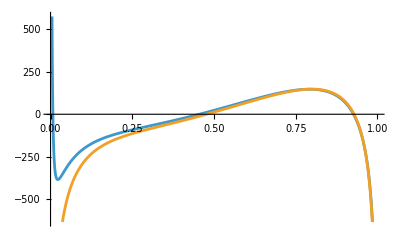

```mathematica
Plot[{c2g2appr[x],1/3*c2g2[x]/.{CF->4/3,CA->3,Zeta2->Zeta[2],Zeta3->Zeta[3],nf->3}},{x,0,1}]
```

```mathematica
X=0.777001;
1/3*c2g2[X]/.{CF->4/3,CA->3,Zeta2->Zeta[2],Zeta3->Zeta[3],nf->3}
c2g2appr[X]
```

145.591+5.4352×10^-15 ⅈ

146.173

```mathematica
X=0.333003;
c2ns2[X]/.{CF->4/3,CA->3,Zeta2->Zeta[2],Zeta3->Zeta[3],nf->3}
c2ns2appr[X]/.nf->3
```

91.368+4.27487×10^-15 ⅈ

92.3285